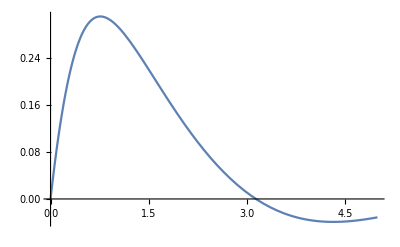

```mathematica
ClearAll["a*","b*","c*"]
f[x_]:=Sin[x]/((x+1)*Sqrt[x^2+1])
a=0.;
b=5.;
gr1=Plot[f[x],{x,a,b}]
```

```mathematica
n=4;
z=f'[a];
X={0.5,1.55,3.2,4.33};
Y=f[X]
data={{a,z},{X[[1]],Y[[1]]},{X[[2]],Y[[2]]},{X[[3]],Y[[3]]},{X[[4]],Y[[4]]}}
```

{0.285874,0.212553,-0.00414561,-0.0391692}

{{0.,1.},{0.5,0.285874},{1.55,0.212553},{3.2,-0.00414561},{4.33,-0.0391692}}

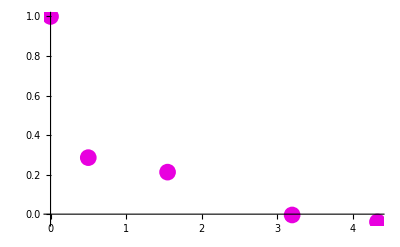

```mathematica
pt1=ListPlot[data,PlotStyle->{PointSize[0.03],Hue[0.84,1,0.91]}];
Print[Show[pt1]];
```

```mathematica
P1[x_]:= a1+b1*x+c1*x^2;

P2[x_]:= a2+b2*x+c2*x^2;
P3[x_]:= a3+b3*x+c3*x^2;

Spl[x_]:=( If[ x<X[[2]], P1[x],
If[x>X[[2]]&&x<X[[3]], P2[x] ,P3[x]]]);
ur1=P1[X[[1]]]==Y[[1]];
ur2=P1[X[[2]]]==Y[[2]];
ur3=P2[X[[2]]]==Y[[2]];
ur4=P2[X[[3]]]==Y[[3]];
ur5=P3[X[[3]]]==Y[[3]];
ur6=P3[X[[4]]]==Y[[4]];

ur7=P1'[X[[2]]]==P2'[X[[2]]];
ur8=P2'[X[[3]]]==P3'[X[[3]]];
ur9=P1'[a]==z;
resh1=Solve[{ur1,ur2,ur3,ur4,ur5,ur6,ur7,ur8,ur9},{a1,b1,c1,a2,b2,c2,a3,b3,c3}]
{a1,b1,c1,a2,b2,c2,a3,b3,c3}={a1,b1,c1,a2,b2,c2,a3,b3,c3}/.resh1[[1]]
```

{{a1→-0.0836588,b1→1.,c1→-0.521868,a2→1.87844,b2→-1.53175,c2→0.294824,a3→-4.63956,b3→2.54201,c3→-0.3417}}

{-0.0836588,1.,-0.521868,1.87844,-1.53175,0.294824,-4.63956,2.54201,-0.3417}

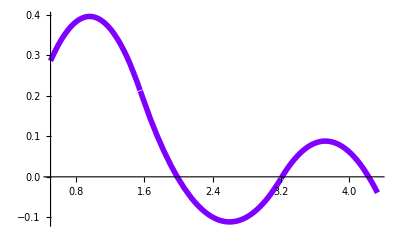

```mathematica
gr222=Plot[ Spl[x] , { x, X[[1]], X[[4]] },PlotStyle->{Hue[0.75], Thickness[0.01]} ]
```

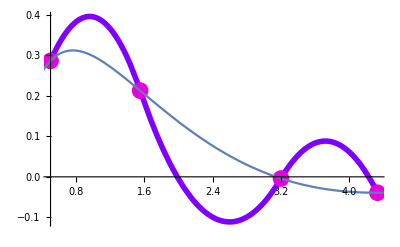

```mathematica
Print[Show[gr222,pt1,gr1]];
```

```mathematica
ClearAll[a1,a2,a3,b1,b2,b3,c1,c2,c3,d1,d2,d3]
```

```mathematica
P11[x_]= a1+b1*x+c1*x^2+d1*x^3;
P21[x_]=a2+b2*x+c2*x^2+d2*x^3;
P31[x_]=a3+b3*x+c3*x^2+d3*x^3;
Ur1=P11[X[[1]]]==Y[[1]];
Ur2=P11[X[[2]]]==Y[[2]];
Ur3=P21[X[[2]]]==Y[[2]];
Ur4=P21[X[[3]]]==Y[[3]];
Ur5=P31[X[[3]]]==Y[[3]];
Ur6=P31[X[[4]]]==Y[[4]];
Ur7=P11'[X[[2]]]==P21'[X[[2]]];
Ur8=P21'[X[[3]]]==P31'[X[[3]]];
Ur9=P11''[X[[2]]]==P21''[X[[2]]];
Ur10=P21''[X[[3]]]==P31''[X[[3]]];
Ur11=P11'[a]==z;
Ur12=P11''[a]==z;
resh2=Solve[{Ur1,Ur2,Ur3,Ur4,Ur5,Ur6,Ur7,Ur8,Ur9,Ur10,Ur11,Ur12},{a1,b1,c1,d1,a2,b2,c2,d2,a3,b3,c3,d3}]
{a1,b1,c1,d1,a2,b2,c2,d2,a3,b3,c3,d3}={a1,b1,c1,d1,a2,b2,c2,d2,a3,b3,c3,d3}/.resh2[[1]]
```

{{a1→-0.262728,b1→1.,c1→0.5,d1→-0.611183,a2→-10.1821,b2→20.1989,c2→-11.8864,d2→2.05255,a3→468.85,b3→-428.894,c3→128.455,d3→-12.5664}}

{-0.262728,1.,0.5,-0.611183,-10.1821,20.1989,-11.8864,2.05255,468.85,-428.894,128.455,-12.5664}

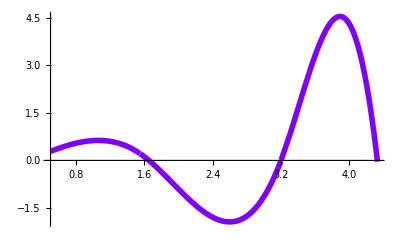

```mathematica
Spl2[x_]:=( If[ x<X[[2]], P11[x],
If[x>X[[2]]&&x<X[[3]], P21[x] ,P31[x]]]);
gr2222=Plot[ Spl2[x] , { x, X[[1]], X[[4]] },PlotStyle->{Hue[0.75], Thickness[0.01]} ]
```

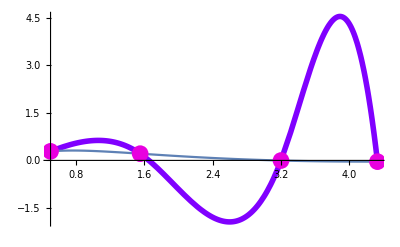

```mathematica
Print[Show[gr2222,gr1,pt1]];
```